```mathematica
years={1669,1735,1748,1751,1753,1766,1771,1772,1774,1774,1781,1782,1783,1789,1789,1791,1794,1798,1798,1801,1802,1803,1803,1803,1803,1804,1807,1807,1808,1808,1808,1808,1808,1811,1817,1817,1817,1824,1825,1825,1829,1830,1838,1842,1842,1844,1860,1861,1861,1863,1875,1878,1879,1879,1879,1879,1880,1885,1885,1886,1886,1886,1894,1895,1898,1898,1898,1898,1898,1899,1901,1906,1913,1919,1922,1937,1939,1940,1940,1940,1944,1944,1945,1949,1950,1952,1952,1955,1961,1966,1969,1970,1974,1981,1984,1994,1996,1999,2000,2002,2003,2003,2010}
```

{1669,1735,1748,1751,1753,1766,1771,1772,1774,1774,1781,1782,1783,1789,1789,1791,1794,1798,1798,1801,1802,1803,1803,1803,1803,1804,1807,1807,1808,1808,1808,1808,1808,1811,1817,1817,1817,1824,1825,1825,1829,1830,1838,1842,1842,1844,1860,1861,1861,1863,1875,1878,1879,1879,1879,1879,1880,1885,1885,1886,1886,1886,1894,1895,1898,1898,1898,1898,1898,1899,1901,1906,1913,1919,1922,1937,1939,1940,1940,1940,1944,1944,1945,1949,1950,1952,1952,1955,1961,1966,1969,1970,1974,1981,1984,1994,1996,1999,2000,2002,2003,2003,2010}

```mathematica
Length@years
```

103

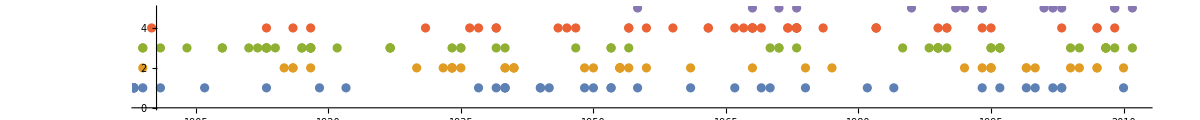

```mathematica
n=55;
ListPlot[#/@years&/@{{#,1}&,{#+n,2}&,{#+2n,3}&,{#+3n,4}&,{#+4n,5}&},AspectRatio->.1,ImageSize->1200,PlotRange->{{1900,2011},All}]
```

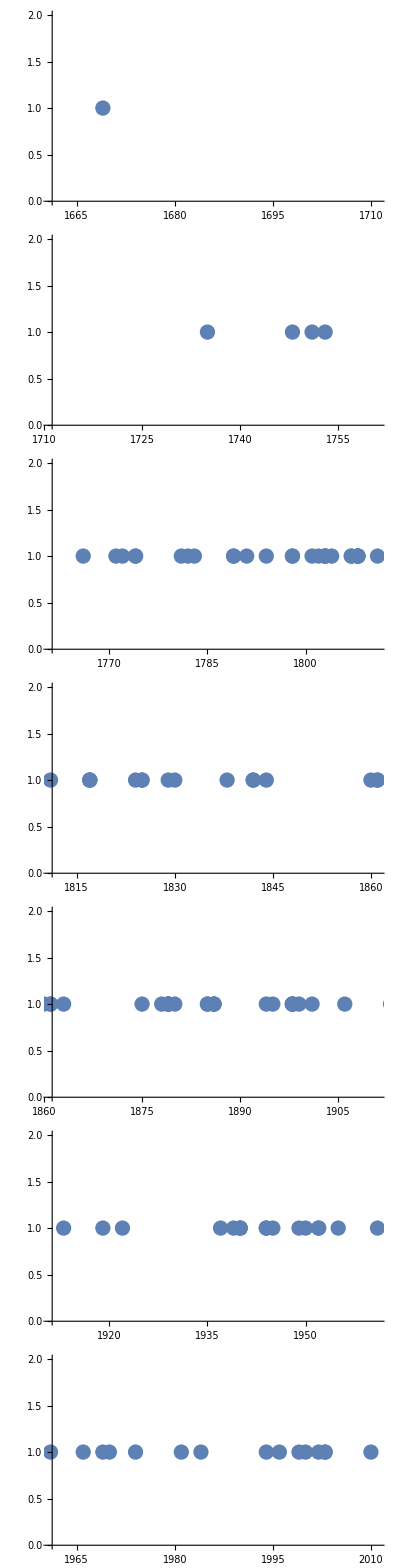

```mathematica
n=50;
Column[Table[ListPlot[{#,1}&/@years,AspectRatio->.05,PlotRange->{{t,t+n},All},ImageSize->1200],{t,2011-Ceiling[(2011-1668)/n]n,2011-n,n}]]
```

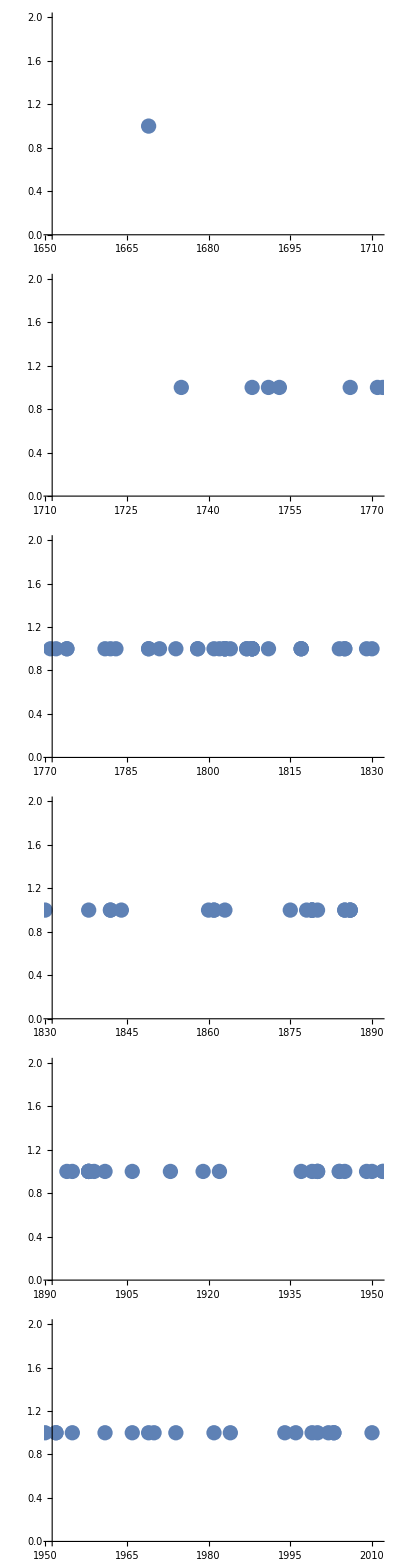

```mathematica
n=60;
Column[Table[ListPlot[{#,1}&/@years,AspectRatio->.05,PlotRange->{{t,t+n},All},ImageSize->1200],{t,2011-Ceiling[(2011-1668)/n]n,2011-n,n}]]
```

```mathematica
(1984-1818)/3.
```

55.3333

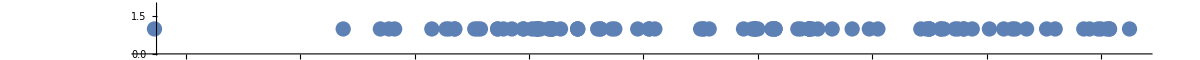

```mathematica
ListPlot[{#,1}&/@years,AspectRatio->.05,PlotRange->{{1668,2011},All},ImageSize->1200]
```

```mathematica
(* conclusion: XX35-XX85 50-yr periods are best, can start in 1735 end 2035 *)
(*1735
14
1785
28
1835
16
1885
17
1935
21
1985
9*)
(* or;
1735 cobalt 15,
1789 Lavoisier 27,
1838 lanthanum 9,
[1869 Mendeleev 11],
1894 argon 13,
1937 technetium 18,
1981 bohrium 12
*)
```